# Quadratic Penalty Methods and Augmented Lagrangians

### Sensitivity: 1D

We are going to look at a 1D inequality constrained optimization problem
		min_(-2≤x≤3) f(x)
and we want to understand what the multipliers mean.

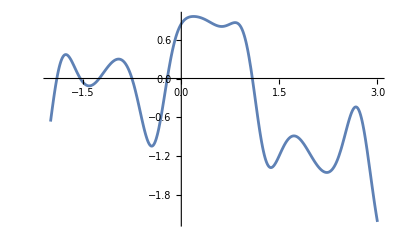

```mathematica
f[x_]:=  Sin[3x+Cos[4x]]-0.2 x^2;
Plot[f[x],{x,-2,3}]
```

We have two inequality constraints.  In our format we have
	x | + | 2 | ≥ | 0
3 | - | x | ≥ | 0
Both end points are KKT points.

For small δ_1 and δ_2 the modified constraint  x+2≥δ_1 and 3-x≥δ_2 gives modified KKT points 
	x_1(δ_1) | = | -2 | + | δ_1
x_2(δ_2) | = | 3 | - | δ_2 
at the modified end points.  Note our sign convention means increasing δ_1 or δ_2 shrinks the feasible set.

Note we could also have
	3x | + | 6 | ≥ | 0
12 | - | 4x | ≥ | 0

```mathematica
c[a_,"+",x_]:=0.5 Which[x<a,(x-a)^2,True,0]
c[a_,"-",x_]:=0.5 Which[x>a,(x-a)^2,True,0]
f[x_]:=  Sin[3x+Cos[4x]]-0.2 x^2;
p[x_]:=c[-2,"+",x]+c[3,"-",x]
Manipulate[
Plot[{f[x],f[x]+μ p[x]},{x, -3,4},PlotRange->{-3.2,1.2},GridLines->Automatic],
{{μ,1},0,100}]
```

At each step we have an x_k and a μ_k.  We get the next point 
	x_(k+1)=argmin g_k+dg_k(x-x_k)+0.5(ddg_k(x-x_k))^2
where 
	g_k | = | f(x_k) | + | μ_k p(x_k)
dg_k | = | df(x_k) | + | μ_k dp(x_k)
ddg_k | = | ddf(x_k) | + | μ_k ddp(x_k)
Then choose μ_(k+1)>μ_k and repeat the process.

```mathematica
g[μ_][x_]:= f[x]+μ p[x]
q[μ_,xk_][x_]:=g[μ][xk]+g[μ]'[xk](x-xk)+0.5g[μ]''[xk](x-xk)^2
Manipulate[
qq[x_]=q[μ,xk][x];
Plot[{f[x],g[μ][x],qq[x]},{x, -3,4},PlotRange->{-3.2,1.2},GridLines->Automatic],
{{μ,10},0,100},
{{xk,-2.1},-3,4}]
```

You choose μ_(k+1)>μ_k to encourage the minimum of the approximating quadratic into the constraint interval if you have a “boundary” minima of f. You quit if you have found an interior minima of f.

We have a decisions to make if the approximating quadratic is not convex i.e. ddg≤0.

In higher dimensions “just go to the edge” is not a feasible computation.

What would be the BFGS, DFP, and Modified Hessian idea?

What would be the SD idea?

What would be the Trust Region idea?

We have a “termination” decision to make.  How do we know we have a KKT point?

We can compute the constrained KKT conditions for f(x).

The constraints are probably not satisfied.  I could write 𝒰 for the set of constraint that are unsatisfied.

As a result, it is not clear what computing the multipliers means.

The unconstrained KKT conditions for g(x)=f(x)+μ p(x) are
	∇g=∇f+μ ∇p=∇f+μ∑_(i∈𝒰) ∇c_i(x)
with 𝒰 indicating the unsatisfied constraints and
	∇c[a,"+",x]=Which[x<a,x-a,True,0]
	∇c[a,"-",x]=Which[x>a,x-a,True,0]

With this quadratic penalty μ ∇c_i is playing the role of a multiplier λ_i

Penalized approximations to original constrained KKT points lie just outside the feasible set.

The penalization parameter needs to be large to make the penalized approximations almost feasible.

#### Ex 2D:

```mathematica
{n,m}={2,5};
f[x_]:=Sin[x⟦1⟧x⟦2⟧-Cos[3x⟦1⟧+x⟦2⟧]-x⟦2⟧]
p[t_]:={Cos[2π(t-0.15)],3 Sin[2 π (t+0.2)]};
normal[t_]:={1,-1}*Reverse[p'[t]]
B=Table[ normal[i/m],{i,1,m}];b=Table[-normal[i/m].p[i/m],{i,1,m}];
{μ,ϵ}={1,0.01};
TabView[{
"cons"->Show[
RegionPlot[Apply[And,Table[B⟦i⟧.{x1,x2}+b⟦i⟧>0,{i,1,m}]],
{x1,-3,3},{x2,-3,3}],
ParametricPlot[p[t],{t,0,1},PlotStyle->Red],
Epilog->{PointSize[0.02],Point[Table[p[i/m],{i,1,m}]]}
],
"3D"->Plot3D[f[{x1,x2}],{x1,-3,3},{x2,-3,3},
PlotLegends->Automatic,
PlotRange->{-2,2},
RegionFunction->Function[{x1,x2},Min[B.{x1,x2}+b]]],
"3D Quad Penalty"->Plot3D[
f[{x1,x2}]+μ Sum[QuadPen[B⟦i⟧.{x1,x2}+b⟦i⟧],{i,1,m}],
{x1,-3,3},{x2,-3,3},
Exclusions->None,
PlotRange->{-2,2}],
"3D Log Barrier"->Plot3D[
f[{x1,x2}]+ϵ Sum[LogBar[B⟦i⟧.{x1,x2}+b⟦i⟧],{i,1,m}],
{x1,-3,3},{x2,-3,3},
PlotRange->{-2,2},
PlotPoints->200,
Exclusions->None]
},2]
```

1234

Summary 
A) Quadratic penalization is smooth but will have computed points that are infeasible. It will also have increasingly badly conditioned linear algebra as the penalization parameter is increased.
B) Abs value penalization is NOT smooth. As the penalization parameter is increased computed point hit the edge of the feasible region. But (and it is a huge but) our techniques do not work on non-smooth problems.
C) Log barrier is smooth and computed points need to be in the feasible region interior. Computed points approach the border of the feasible set as the barrier parameter ϵ is decreased. It is possible to exploit the simple explicit gradient 
	∇_x (∑_(k=1)^m LogBar[c_i(x)])=-∑_(k=1)^m 1/(c_i(x))∇c_i(x)
to partially separate the constraint and cost function computations.   This is the basis of Interior Point Methods.

### Quadratic Penalization: 1D

We are going to build a 1D Quadratic Penalty Newton method.

Quadratic Penalization refers to adding a piecewise quadratic penalty term to an objective function f to enforce 
(or maybe just encourage) satisfaction of a constraint.  For inequality constraints this technique allows non-feasible 
points and requires large values of the penalization parameter. We are going to do a 1D problem
	min_(-2≤x≤3) f(x)
with an updating local quadratic approximation
	f(x)≈ f_k+df_k(x-x_k)+0.5(ddf_k(x-x_k))^2
Our standard quadratic penalty term is μ_k p(x) where
	p(x)=c(-2,"+",x)+c(3,"-",x)
where 
	c(a,"+",x)=0.5{(x-a)^2 | if | x<a
0 | if | x≥a	 
and 
	c(a,"-",x)=0.5{(x-a)^2 | if | x>a
0 | if | x≤a

```mathematica
c[a_,"+",x_]:=0.5 Which[x<a,(x-a)^2,True,0]
c[a_,"-",x_]:=0.5 Which[x>a,(x-a)^2,True,0]
f[x_]:=  Sin[3x+Cos[4x]]-0.2 x^2;
p[x_]:=c[-2,"+",x]+c[3,"-",x]
Manipulate[
Plot[{f[x],f[x]+μ p[x]},{x, -3,4},PlotRange->{-3.2,1.2},GridLines->Automatic],
{{μ,1},0,100}]
```

At each step we have an x_k and a μ_k.  We get the next point 
	x_(k+1)=argmin g_k+dg_k(x-x_k)+0.5(ddg_k(x-x_k))^2
where 
	g_k | = | f(x_k) | + | μ_k p(x_k)
dg_k | = | df(x_k) | + | μ_k dp(x_k)
ddg_k | = | ddf(x_k) | + | μ_k ddp(x_k)
Then choose μ_(k+1)>μ_k and repeat the process.

```mathematica
g[μ_][x_]:= f[x]+μ p[x]
q[μ_,xk_][x_]:=g[μ][xk]+g[μ]'[xk](x-xk)+0.5g[μ]''[xk](x-xk)^2
Manipulate[
qq[x_]=q[μ,xk][x];
Plot[{f[x],g[μ][x],qq[x]},{x, -3,4},PlotRange->{-3.2,1.2},GridLines->Automatic],
{{μ,10},0,100},
{{xk,-2.1},-3,4}]
```

You choose μ_(k+1)>μ_k to encourage the minimum of the approximating quadratic into the constraint interval if you have a “boundary” minima of f. You quit if you have found an interior minima of f.

We have a decisions to make if the approximating quadratic is not convex i.e. ddg≤0.

In higher dimensions “just go to the edge” is not a feasible computation.

What would be the BFGS, DFP, and Modified Hessian idea?

What would be the SD idea?

What would be the Trust Region idea?

We have a “termination” decision to make.  How do we know we have a KKT point?

We can compute the constrained KKT conditions for f(x).

The constraints are probably not satisfied.  I could write 𝒰 for the set of constraint that are unsatisfied.

As a result, it is not clear what computing the multipliers means.

The unconstrained KKT conditions for g(x)=f(x)+μ p(x) are
	∇g=∇f+μ ∇p=∇f+μ∑_(i∈𝒰) ∇c_i(x)
with 𝒰 indicating the unsatisfied constraints and
	∇c[a,"+",x]=Which[x<a,x-a,True,0]
	∇c[a,"-",x]=Which[x>a,x-a,True,0]

With this quadratic penalty μ ∇c_i is playing the role of a multiplier λ_i

Penalized approximations to original constrained KKT points lie just outside the feasible set.

The penalization parameter needs to be large to make the penalized approximations almost feasible.

#### Ex 2D:

```mathematica
{n,m}={2,5};
f[x_]:=Sin[x⟦1⟧x⟦2⟧-Cos[3x⟦1⟧+x⟦2⟧]-x⟦2⟧]
p[t_]:={Cos[2π(t-0.15)],3 Sin[2 π (t+0.2)]};
normal[t_]:={1,-1}*Reverse[p'[t]]
B=Table[ normal[i/m],{i,1,m}];b=Table[-normal[i/m].p[i/m],{i,1,m}];
{μ,ϵ}={1,0.01};
TabView[{
"cons"->Show[
RegionPlot[Apply[And,Table[B⟦i⟧.{x1,x2}+b⟦i⟧>0,{i,1,m}]],
{x1,-3,3},{x2,-3,3}],
ParametricPlot[p[t],{t,0,1},PlotStyle->Red],
Epilog->{PointSize[0.02],Point[Table[p[i/m],{i,1,m}]]}
],
"3D"->Plot3D[f[{x1,x2}],{x1,-3,3},{x2,-3,3},
PlotLegends->Automatic,
PlotRange->{-2,2},
RegionFunction->Function[{x1,x2},Min[B.{x1,x2}+b]]],
"3D Quad Penalty"->Plot3D[
f[{x1,x2}]+μ Sum[QuadPen[B⟦i⟧.{x1,x2}+b⟦i⟧],{i,1,m}],
{x1,-3,3},{x2,-3,3},
Exclusions->None,
PlotRange->{-2,2}],
"3D Log Barrier"->Plot3D[
f[{x1,x2}]+ϵ Sum[LogBar[B⟦i⟧.{x1,x2}+b⟦i⟧],{i,1,m}],
{x1,-3,3},{x2,-3,3},
PlotRange->{-2,2},
PlotPoints->200,
Exclusions->None]
},2]
```

1234

Summary 
A) Quadratic penalization is smooth but will have computed points that are infeasible. It will also have increasingly badly conditioned linear algebra as the penalization parameter is increased.
B) Abs value penalization is NOT smooth. As the penalization parameter is increased computed point hit the edge of the feasible region. But (and it is a huge but) our techniques do not work on non-smooth problems.
C) Log barrier is smooth and computed points need to be in the feasible region interior. Computed points approach the border of the feasible set as the barrier parameter ϵ is decreased. It is possible to exploit the simple explicit gradient 
	∇_x (∑_(k=1)^m LogBar[c_i(x)])=-∑_(k=1)^m 1/(c_i(x))∇c_i(x)
to partially separate the constraint and cost function computations.   This is the basis of Interior Point Methods.

### Multiplier Interpretation: 2D

With a 2D quadratic model with linear constraints we can see exactly what multipliers do.

```mathematica
Clear[c]
n=2;
A=RandomReal[{-1,1},{2,2}];A=A+Aᵀ; g=RandomReal[{-1,1},n];
B[1]={-1,1};B[2]={2,-1};B[3]={3,1};B[4]={-3,-2};
c[{b1_,b2_,b3_,b4_}][{x1_,x2_}]:= And[B[1].{x1,x2}>b1,B[2].{x1,x2}>b2, B[3].{x1,x2}>b3,B[4].{x1,x2}>b4]
f[x_]:=0.5 x.A.x+g.x
Manipulate[
ContourPlot[f[{x1,x2}],{x1,-0.6,0.8},{x2,-1.1,1.1},
Contours->30,
ContourLabels->True,
RegionFunction->Function[{x1,x2},c[{b1,b2,b3,b4}][{x1,x2}]]],
{{b1,-1},-1.2,-0.8},
{{b2,-1},-1.2,-0.8},
{{b3,-1},-1.2,-0.8},
{{b4,-2},-2.1,-1.9}]
```

Complementary slackness means

λ_i c_i[x]=0 for all i

If λ_i=0 and c_i[x]=0 then the constraint is not “strictly complementary”

A “strictly complementary” has non-zero multiplier.

If c_i[x]≥0 is “strictly complementary” then with the slightly different inequality constraint c_i[x]≥δ the minimum is different

If c_i[x]=0 is “strictly complementary” then with the slightly different equality constraint c_i[x]=δ the minimum is different.

Lagrange multipliers describe how sensitive the minimum is to perturbations in each constraint.  This is our target for today

In 2D I have a maximum of 2 genuinely active constraints.

2 active constraints. “Corner”

1 active constraint. “Edge”

## Ex 2D:

```mathematica
{n,m}={2,5};
f[x_]:=Sin[x⟦1⟧x⟦2⟧-Cos[3x⟦1⟧+x⟦2⟧]-x⟦2⟧]
p[t_]:={Cos[2π(t-0.15)],3 Sin[2 π (t+0.2)]};
normal[t_]:={1,-1}*Reverse[p'[t]]
B=Table[ normal[i/m],{i,1,m}];b=Table[-normal[i/m].p[i/m],{i,1,m}];
{μ,ϵ}={1,0.01};
TabView[{
"cons"->Show[
RegionPlot[Apply[And,Table[B⟦i⟧.{x1,x2}+b⟦i⟧>0,{i,1,m}]],
{x1,-3,3},{x2,-3,3}],
ParametricPlot[p[t],{t,0,1},PlotStyle->Red],
Epilog->{PointSize[0.02],Point[Table[p[i/m],{i,1,m}]]}
],
"3D"->Plot3D[f[{x1,x2}],{x1,-3,3},{x2,-3,3},
PlotLegends->Automatic,
PlotRange->{-2,2},
RegionFunction->Function[{x1,x2},Min[B.{x1,x2}+b]]],
"3D Quad Penalty"->Plot3D[
f[{x1,x2}]+μ Sum[QuadPen[B⟦i⟧.{x1,x2}+b⟦i⟧],{i,1,m}],
{x1,-3,3},{x2,-3,3},
Exclusions->None,
PlotRange->{-2,2}],
"3D Log Barrier"->Plot3D[
f[{x1,x2}]+ϵ Sum[LogBar[B⟦i⟧.{x1,x2}+b⟦i⟧],{i,1,m}],
{x1,-3,3},{x2,-3,3},
PlotRange->{-2,2},
PlotPoints->200,
Exclusions->None]
},2]
```

1234

Summary 
A) Quadratic penalization is smooth but will have computed points that are infeasible. It will also have increasingly badly conditioned linear algebra as the penalization parameter is increased.
B) Abs value penalization is NOT smooth. As the penalization parameter is increased computed point hit the edge of the feasible region. But (and it is a huge but) our techniques do not work on non-smooth problems.
C) Log barrier is smooth and computed points need to be in the feasible region interior. Computed points approach the border of the feasible set as the barrier parameter ϵ is decreased. It is possible to exploit the simple explicit gradient 
	∇_x (∑_(k=1)^m LogBar[c_i(x)])=-∑_(k=1)^m 1/(c_i(x))∇c_i(x)
to partially separate the constraint and cost function computations.   This is the basis of Interior Point Methods.

## KKT Reminder

The equations that give solutions to 
	min_(x∈Ω) f(x)
where the feasible set is 
	Ω={x∈ℝ^n withc_i(x)≥0 | for i∈ℐ }
are in terms of the Lagrangian ℒ(x,λ)=f(x)-∑_(i∈ℐ) λ_i c_i(x) are

∇_x ℒ(x,λ)=∇f(x)-∑_(i∈ℐ) λ_i∇c_i(x)=0_n

c_i(x)≥0 and λ_i≥0 for i∈ℐ 	“satisfies inequality constraints with positive Lagrange multipliers”

λ_i c_i(x)=0 for i∈ℐ		“inactive constraints have zero multipliers”

Our target is to find an iteration that produces a sequence of feasible points,  reduces f(x) at each step, and converges to a KKT point.

#### For i∈ℐ we need λ_i c_i=0 “Complementary Slackness” Relaxing “Complementary Slackness”

The sets λ c=σ look pretty close to the set λ c=0 provided σ is small.  Relaxing complementary slackness means replacing λ c=0 with λ c=σ and letting σ↘0.

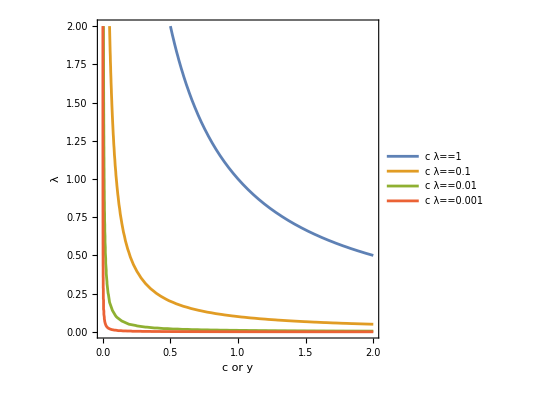

```mathematica
ContourPlot[{λ c ==1,λ c ==0.1,λ c ==0.01,λ c == 0.001},
{c,0,2},{λ,0,2},
FrameLabel->{"c or y","λ"},
PlotLegends->"Expressions"]
```

The connection with the log barrier formulation is that if λ c=σ the gradient 
	∇_x (-log(c))=-1/c∇_x c = -σ λ ∇_x c
which is quadratic.  Since Newton’s method is well suited to quadratic terms like this the log-barrier formulation generates practical algorithms.  These algorithms can be developed from log-barrier formulations but they are usually developed in linear algebraic language.

## Interior Point Notation for 16.6 p480 LCQP - Linearly Constrained Quadratic Program

For no apparent reason our book has changed notation!
	min_x 0.5 x.G.x+c.x
subject to 
	A.x≥b
where G=Gᵀ is an n×n matrix, b is an n vector, A is an m×n vector, and b is an m vector. We (and the book) are going to stick with this.  The KKT equations simplify to

G.x+c-Aᵀ.λ=0  	from ∇_x ℒ(x,λ)=∇f(x)-∑_(i∈ℐ) λ_i∇c_i(x)=0_n

A[i,:].x≥b_i for 1≤i≤m	“constraints satisfied”

λ_i≥0 for 1≤i≤m 	“non-negative Lagrange multipliers”

λ_i c_i(x)=0 for 1≤i≤m	“inactive constraints have zero multipliers”

It is standard to get rid of the inequalities by creating an m vector of positive slack variables
	y=A.x-b≥0_m
It is standard to write all of this as vectors in which case we get the system

G.x+c-Aᵀ.λ=0_n

A.x-y-b=0_m

λ≥0_m	“non-negative Lagrange multipliers”

y≥0_m	“non-negative slack variables”

y_i λ_i=0	“inactive constraints are off

Our target is to find an iteration 
	(x_k,y_k,λ_k)⟶ (x_(k+1),y_(k+1),λ_(k+1))
that satisfies the first four of these conditions and has “complementary measure” 
	μ_k=(y_k.λ_k)/m⟶0
going to zero as k→∞. In words, it produces feasible points with appropriate multipliers that approach the “complementary slackness” condition in the KKT equations.  If we can do this then we can eventually satisfy the KKT conditions as accurately as we want. In other words, we can find KKT points.

## Perturbed Interior Point Equations LCQP §16.6 p481

Our target is a stack of “almost linear algebra” equations.  Look at
	F((x,y,λ);σ,μ)=(G.x-Aᵀ.λ+c
A.x-y-b
𝒴.Λ(.1)_m-σ μ 1_m)
where 
	𝒴=(y_1 | 0 | ⋯ |   | 0
0 | y_2 |   |   | ⋮
⋮ |   | ⋱ |   |  
  |   |   | y_(m-1) | 0
0 | ⋯ |   | 0 | y_m), Λ=(λ_1 | 0 | ⋯ |   | 0
0 | λ_2 |   |   | ⋮
⋮ |   | ⋱ |   |  
  |   |   | λ_(m-1) | 0
0 | ⋯ |   | 0 | λ_m) and 1_m=(1
1
⋮
 
1).
for fixed σ and μ we can apply Newton’s method to the slightly nonlinear function F:ℝ^(n+m+m)→ℝ^(n+m+m) to start solving F((x,y,λ):σ,μ)=0_(n+2m).  Writing z=(x,y,λ)∈ℝ^(n+2m) for the concatenated vector we have
	∇_z F=(G | 0 | -Aᵀ
A | -I | 0
0 | Λ | 𝒴) .
One step of a Newton iteration that would converge with a decent initial condition would be
	z_(n+1)=z_n+Δz
where Δz=(Δx,Δy,Δz) satisfies 
(M)	(G | 0 | -Aᵀ
A | -I | 0
0 | Λ | 𝒴)(Δx
Δy
Δλ)=(-(G.x-Aᵀ.λ+c)
-(A.x-y-b)
-Λ.𝒴(.1)_n+σ μ 1_n).
The problem is that that y_n+Δy and λ_n+Δλ may not have all positive entries even though y_n and λ_n do. The standard solution is to restrict the step by finding an α<1 so that 
	z_(n+1)=(x_(n+1),y_(n+1)^+,λ_(n+1)^+)=(x_n,y_n,λ_n)+α(Δx,Δy,Δy)
is feasible i.e. y_(n+1)^+ and λ_(n+1)^+ have all positive entries.

The discussion of efficiently solving equation (M) focuses on G SPD in which case this is a Linearly Constrained Convex Quadratic Program.

I am going to implement Algorithm 16.4 on page 484.